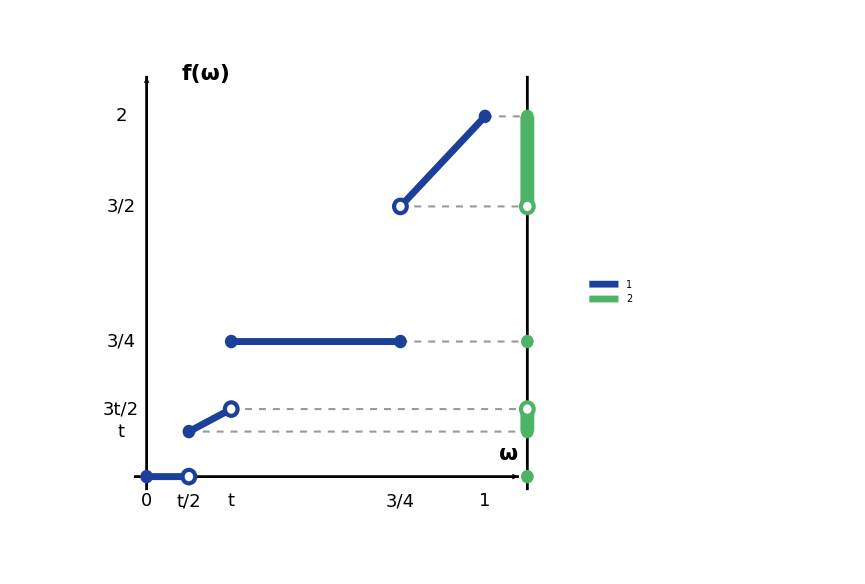

```mathematica
ClearAll[colF, colIm, r, xC, cerrado, abierto, ejes, trozos, guias, ejeCod, etiquetas, grafico1,
  diagrama1];

colF = RGBColor[0.1, 0.25, 0.6];     (* gráfica de f *)
colIm = RGBColor[0.3, 0.7, 0.4];     (* imagen de f *)
r = 0.3;
xC = 18;                             (* eje del codominio, a la derecha *)

cerrado[p_, col_] := {col, Disk[p, r]};
abierto[p_, col_] := {White, Disk[p, r], col, AbsoluteThickness[3], Circle[p, r]};

(* escala del dibujo (t = 1/4): horizontal 16 por unidad de ω, vertical 8 por unidad de f *)
ejes = {Black, AbsoluteThickness[2], Arrowheads[0.025],
   Arrow[{{-0.6, 0}, {17.6, 0}}], Arrow[{{0, -0.6}, {0, 17.8}}]};

trozos = {colF, AbsoluteThickness[5],
   Line[{{0, 0}, {2, 0}}], Line[{{2, 2}, {4, 3}}],
   Line[{{4, 6}, {12, 6}}], Line[{{12, 12}, {16, 16}}],
   cerrado[{0, 0}, colF], abierto[{2, 0}, colF],
   cerrado[{2, 2}, colF], abierto[{4, 3}, colF],
   cerrado[{4, 6}, colF], cerrado[{12, 6}, colF],
   abierto[{12, 12}, colF], cerrado[{16, 16}, colF]};

guias = {GrayLevel[0.6], Dashed, AbsoluteThickness[1.5],
   Line[{{2, 2}, {xC, 2}}], Line[{{4, 3}, {xC, 3}}], Line[{{12, 6}, {xC, 6}}],
   Line[{{12, 12}, {xC, 12}}], Line[{{16, 16}, {xC, 16}}]};

(* imagen de f = {0} ∪ [t, 3t/2) ∪ {3/4} ∪ (3/2, 2] *)
ejeCod = {Black, AbsoluteThickness[2], Line[{{xC, -0.6}, {xC, 17.8}}],
   colIm, AbsoluteThickness[10], CapForm["Butt"],
   Line[{{xC, 2}, {xC, 3}}], Line[{{xC, 12}, {xC, 16}}],
   cerrado[{xC, 0}, colIm], cerrado[{xC, 2}, colIm], abierto[{xC, 3}, colIm],
   cerrado[{xC, 6}, colIm], abierto[{xC, 12}, colIm], cerrado[{xC, 16}, colIm]};

etiquetas = {Black,
   Table[Text[Style[p[[2]], 18], {p[[1]], -1.1}],
    {p, {{0, "0"}, {2, "t/2"}, {4, "t"}, {12, "3/4"}, {16, "1"}}}],
   Table[Text[Style[p[[2]], 18], {-1.2, p[[1]]}],
    {p, {{2, "t"}, {3, "3t/2"}, {6, "3/4"}, {12, "3/2"}, {16, "2"}}}],
   Text[Style["ω", 22, Bold], {17.1, 1.0}],
   Text[Style["f(ω)", 22, Bold], {2.8, 17.9}]};

grafico1 = Graphics[{guias, ejes, trozos, ejeCod, etiquetas},
   PlotRange -> {{-3.4, 19.8}, {-2.4, 18.8}}, ImageSize -> 640];

diagrama1 = Legended[grafico1,
   SwatchLegend[{colF, colIm}, {"gráfica de f", "imagen de f"},
    LabelStyle -> Directive[FontSize -> 24], LegendMarkerSize -> 20]];

diagrama1

Export[CloudObject["T2_P50_funcion"], diagrama1,"PNG", Background -> None,
  ImageResolution -> 640];
```

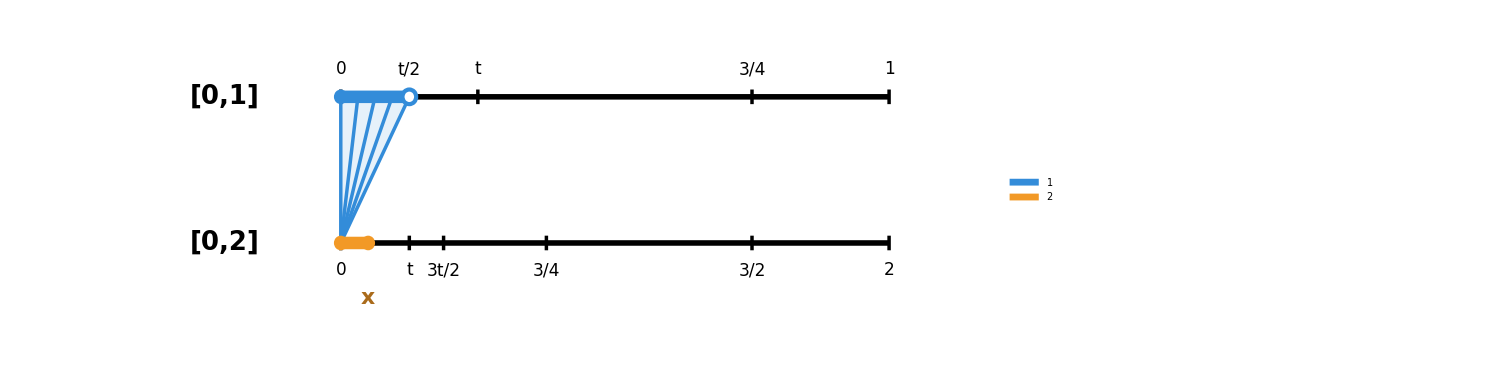
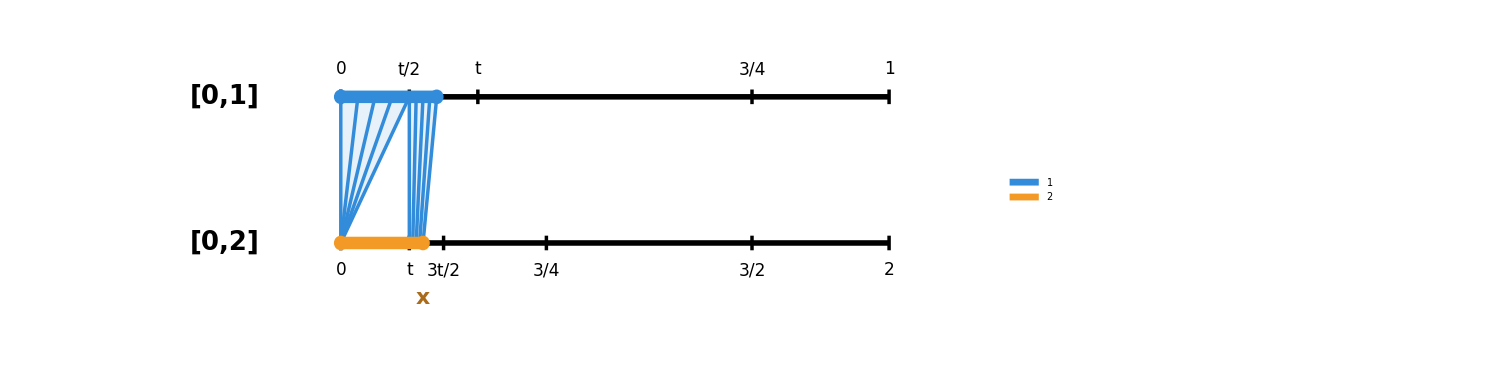
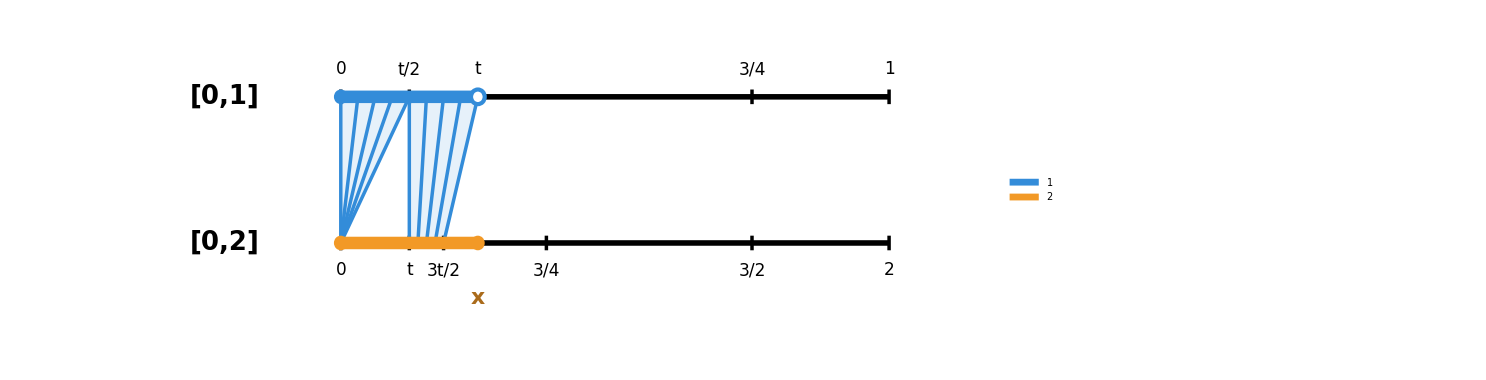
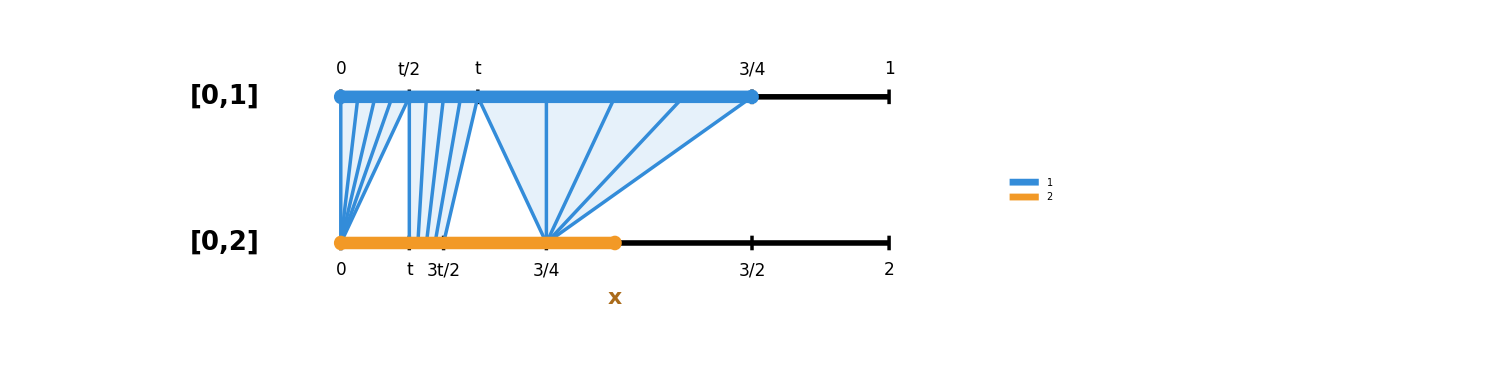
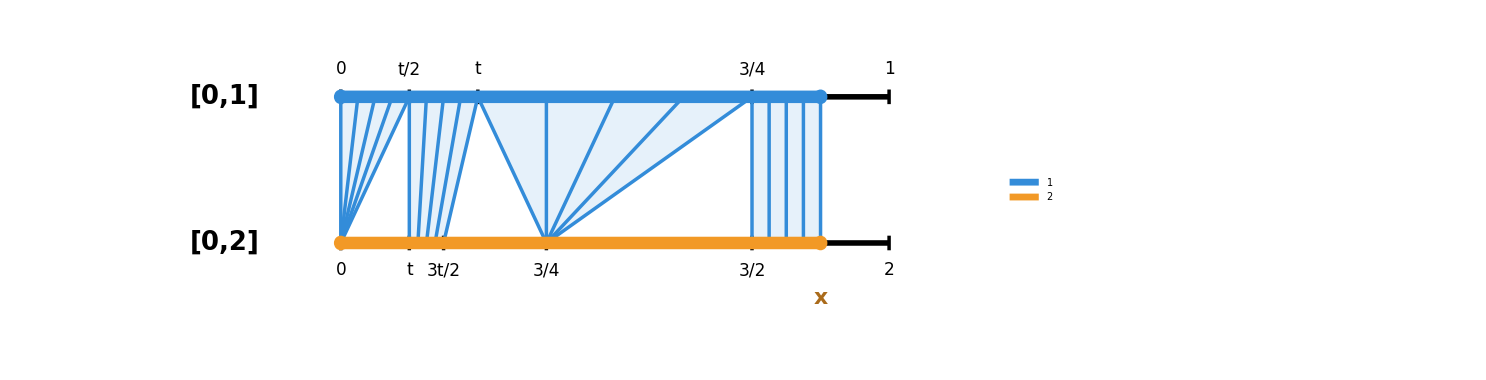

```mathematica
ClearAll[yTop, yBot, colO, colN, rr, cerrado, abierto, baseArriba, baseAbajo, pieza, segTop,
  intervaloAbajo, leyenda, caso, casos];

yTop = 4; yBot = 0;
colO = RGBColor[0.2, 0.55, 0.85];    (* antiimagen, en [0,1] *)
colN = RGBColor[0.95, 0.6, 0.15];    (* intervalo [0,x], en [0,2] *)
rr = 0.2;

cerrado[p_, col_] := {col, Disk[p, rr]};
abierto[p_, col_] := {White, Disk[p, rr], col, AbsoluteThickness[3], Circle[p, rr]};

(* [0,1] se dibuja con escala 16 y [0,2] con escala 8, así ocupan el mismo ancho *)
baseArriba = {
   {Black, AbsoluteThickness[4], Line[{{0, yTop}, {16, yTop}}]},
   Table[{Black, AbsoluteThickness[2.5], Line[{{p[[1]], yTop - 0.2}, {p[[1]], yTop + 0.2}}],
     Text[Style[p[[2]], 17], {p[[1]], yTop + 0.75}]},
    {p, {{0, "0"}, {2, "t/2"}, {4, "t"}, {12, "3/4"}, {16, "1"}}}],
   Text[Style["[0,1]", 26, Bold], {-3.4, yTop}]};

baseAbajo = {
   {Black, AbsoluteThickness[4], Line[{{0, yBot}, {16, yBot}}]},
   Table[{Black, AbsoluteThickness[2.5], Line[{{p[[1]], yBot - 0.2}, {p[[1]], yBot + 0.2}}],
     Text[Style[p[[2]], 17], {p[[1]], yBot - 0.75}]},
    {p, {{0, "0"}, {2, "t"}, {3, "3t/2"}, {6, "3/4"}, {12, "3/2"}, {16, "2"}}}],
   Text[Style["[0,2]", 26, Bold], {-3.4, yBot}]};

(* un tramo de la antiimagen: de {t1,t2} arriba a {b1,b2} abajo; si b1 = b2 es un abanico *)
pieza[t1_, t2_, b1_, b2_] := {
   {colO, Opacity[0.12], Polygon[{{t1, yTop}, {t2, yTop}, {b2, yBot}, {b1, yBot}}]},
   {colO, AbsoluteThickness[2.5],
    Table[Line[{{t1 + s (t2 - t1), yTop}, {b1 + s (b2 - b1), yBot}}],
     {s, {0, 0.25, 0.5, 0.75, 1}}]}};

(* la antiimagen sobre [0,1]: empieza en 0 (cerrado) y termina en fin *)
segTop[fin_, cerr_] := {colO, AbsoluteThickness[9], CapForm["Butt"],
   Line[{{0, yTop}, {fin, yTop}}],
   cerrado[{0, yTop}, colO],
   If[cerr, cerrado[{fin, yTop}, colO], abierto[{fin, yTop}, colO]]};

(* el intervalo [0,x] sobre [0,2] *)
intervaloAbajo[xb_] := {colN, AbsoluteThickness[9], CapForm["Butt"],
   Line[{{0, yBot}, {xb, yBot}}],
   cerrado[{0, yBot}, colN], cerrado[{xb, yBot}, colN],
   Text[Style["x", 22, Bold, Darker[colN, 0.3]], {xb, yBot - 1.5}]};

leyenda = SwatchLegend[{colO, colN}, {"antiimagen", "intervalo [0,x]"},
   LabelStyle -> Directive[FontSize -> 18], LegendMarkerSize -> 20];

caso[xb_, finTop_, cerrFin_, piezas_List] := Legended[
   Graphics[{baseArriba, baseAbajo,
     Table[pieza @@ p, {p, piezas}],
     segTop[finTop, cerrFin], intervaloAbajo[xb]},
    PlotRange -> {{-6.2, 18.4}, {yBot - 2.8, yTop + 1.7}}, ImageSize -> 1100],
   leyenda];

(* tramos: {arriba1, arriba2, abajo1, abajo2}.
   tramo 1: [0,t/2) -> 0   tramo 2: [t/2,t) -> [t,3t/2)
   tramo 3: [t,3/4] -> 3/4   tramo 4: (3/4,1] -> (3/2,2] *)
casos = {
   caso[0.8, 2, False, {{0, 2, 0, 0}}],                                                  (* 0 <= x < t *)
   caso[2.4, 2.8, True, {{0, 2, 0, 0}, {2, 2.8, 2, 2.4}}],                               (* t <= x < 3t/2 *)
   caso[4, 4, False, {{0, 2, 0, 0}, {2, 4, 2, 3}}],                                      (* 3t/2 <= x < 3/4 *)
   caso[8, 12, True, {{0, 2, 0, 0}, {2, 4, 2, 3}, {4, 12, 6, 6}}],                       (* 3/4 <= x <= 3/2 *)
   caso[14, 14, True, {{0, 2, 0, 0}, {2, 4, 2, 3}, {4, 12, 6, 6}, {12, 14, 12, 14}}]};   (* 3/2 < x <= 2 *)

casos

(* se guardan como T2_P50_a1.png, ..., T2_P50_a5.png *)
Do[Export[CloudObject["T2_P50_a" <> ToString[k]], casos[[k]],"PNG", Background -> None,
   ImageResolution -> 600], {k, 1, 5}];
```

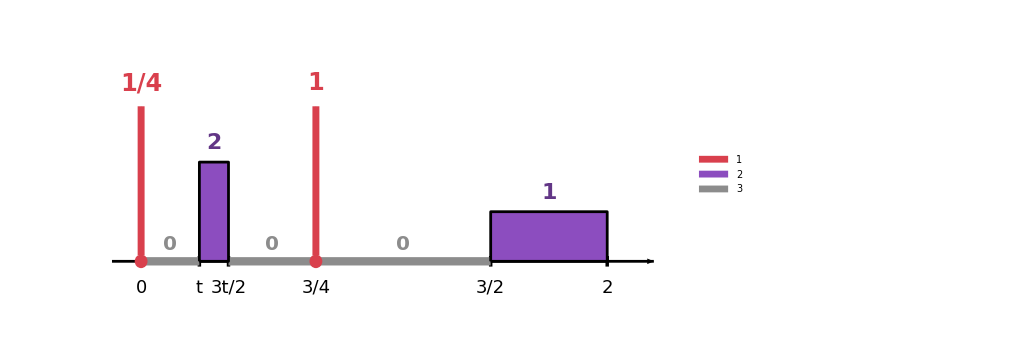

```mathematica
ClearAll[colDens, colAt, colCero, hD, yA, r, ejeBase, dens, ceros, atomos, grafico3, diagrama3];

colDens = RGBColor[0.55, 0.3, 0.75];
colAt = RGBColor[0.85, 0.25, 0.3];
colCero = GrayLevel[0.55];
hD = 1.6;     (* altura que representa densidad 1 *)
yA = 5;       (* altura (solo gráfica) de las flechas de masa puntual *)
r = 0.22;

ejeBase = {Black, AbsoluteThickness[2], Arrowheads[0.025], Arrow[{{-1, 0}, {17.6, 0}}],
   Table[{Black, AbsoluteThickness[2.5], Line[{{p[[1]], -0.17}, {p[[1]], 0.17}}],
     Text[Style[p[[2]], 18], {p[[1]], -0.85}]},
    {p, {{0, "0"}, {2, "t"}, {3, "3t/2"}, {6, "3/4"}, {12, "3/2"}, {16, "2"}}}]};

(* densidad 2 en [t,3t/2) y densidad 1 en (3/2,2] *)
dens = {colDens, EdgeForm[{Black, AbsoluteThickness[2]}],
   Rectangle[{2, 0}, {3, 2 hD}], Rectangle[{12, 0}, {16, hD}],
   Darker[colDens, 0.3],
   Text[Style["2", 22, Bold], {2.5, 2 hD + 0.6}],
   Text[Style["1", 22, Bold], {14, hD + 0.6}]};

(* masa 0 en los huecos *)
ceros = {colCero, AbsoluteThickness[6], CapForm["Butt"],
   Line[{{0, 0}, {2, 0}}], Line[{{3, 0}, {12, 0}}],
   Text[Style["0", 20, Bold, colCero], {1, 0.55}],
   Text[Style["0", 20, Bold, colCero], {4.5, 0.55}],
   Text[Style["0", 20, Bold, colCero], {9, 0.55}]};

(* masas puntuales: 1/4 en el 0 y 1 en el 3/4 *)
atomos = {
   {colAt, AbsoluteThickness[5], Arrowheads[0.035], Arrow[{{0, 0.2}, {0, yA}}],
    Disk[{0, 0}, r], Text[Style["1/4", 24, Bold, colAt], {0, yA + 0.75}]},
   {colAt, AbsoluteThickness[5], Arrowheads[0.035], Arrow[{{6, 0.2}, {6, yA}}],
    Disk[{6, 0}, r], Text[Style["1", 24, Bold, colAt], {6, yA + 0.75}]}};

grafico3 = Graphics[{ejeBase, dens, ceros, atomos},
   PlotRange -> {{-1.8, 18.2}, {-1.8, 7.4}}, ImageSize -> 760];

diagrama3 = Legended[grafico3,
   SwatchLegend[{colAt, colDens, colCero}, {"masa puntual", "densidad", "masa 0"},
    LabelStyle -> Directive[FontSize -> 24], LegendMarkerSize -> 20]];

diagrama3

Export[CloudObject["T2_P50_b1"], diagrama3,"PNG", Background -> None,
  ImageResolution -> 760];
```

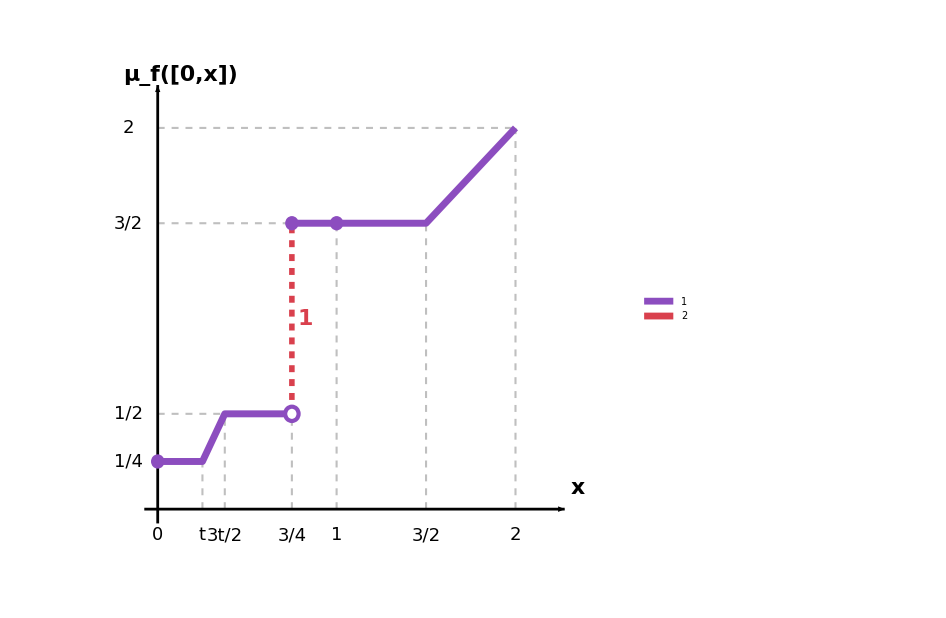

```mathematica
ClearAll[colCDF, colSalto, r, cerrado, abierto, ejes, guiasV, guiasH, curva, salto, puntos,
  etiquetas, grafico4, diagrama4];

colCDF = RGBColor[0.55, 0.3, 0.75];
colSalto = RGBColor[0.85, 0.25, 0.3];
r = 0.3;

cerrado[p_, col_] := {col, Disk[p, r]};
abierto[p_, col_] := {White, Disk[p, r], col, AbsoluteThickness[3], Circle[p, r]};

(* escala del dibujo: horizontal 8 por unidad de x, vertical 8 por unidad de valor *)
ejes = {Black, AbsoluteThickness[2], Arrowheads[0.025],
   Arrow[{{-0.6, 0}, {18.2, 0}}], Arrow[{{0, -0.6}, {0, 17.8}}]};

guiasV = {GrayLevel[0.75], Dashed, AbsoluteThickness[1.5],
   Table[Line[{{p[[1]], 0}, p}], {p, {{2, 2}, {3, 4}, {6, 4}, {8, 12}, {12, 12}, {16, 16}}}]};
guiasH = {GrayLevel[0.75], Dashed, AbsoluteThickness[1.5],
   Line[{{0, 4}, {3, 4}}], Line[{{0, 12}, {6, 12}}], Line[{{0, 16}, {16, 16}}]};

(* 1/4 en [0,t); sube hasta 1/2 en [t,3t/2); 1/2 hasta 3/4; salta a 3/2; llega a 2 *)
curva = {colCDF, AbsoluteThickness[5],
   Line[{{0, 2}, {2, 2}, {3, 4}, {6, 4}}],
   Line[{{6, 12}, {12, 12}, {16, 16}}]};

(* el salto en x = 3/4 es la masa puntual de ese punto *)
salto = {colSalto, Dashed, AbsoluteThickness[4], Line[{{6, 4}, {6, 12}}]};

puntos = {cerrado[{0, 2}, colCDF], abierto[{6, 4}, colCDF], cerrado[{6, 12}, colCDF],
   cerrado[{8, 12}, colCDF]};

etiquetas = {Black,
   Table[Text[Style[p[[2]], 18], {p[[1]], -1.1}],
    {p, {{0, "0"}, {2, "t"}, {3, "3t/2"}, {6, "3/4"}, {8, "1"}, {12, "3/2"}, {16, "2"}}}],
   Table[Text[Style[p[[2]], 18], {-1.3, p[[1]]}],
    {p, {{2, "1/4"}, {4, "1/2"}, {12, "3/2"}, {16, "2"}}}],
   Text[Style["x", 22, Bold], {18.8, 0.9}],
   Text[Style[Row[{Subscript["μ", "f"], "([0,x])"}], 22, Bold], {1.0, 18.2}, {-1, 0}],
   Text[Style["1", 22, Bold, colSalto], {6.6, 8}, {-1, 0}]};

grafico4 = Graphics[{guiasV, guiasH, ejes, salto, curva, puntos, etiquetas},
   PlotRange -> {{-3.4, 20.6}, {-2.2, 19.0}}, ImageSize -> 700];

diagrama4 = Legended[grafico4,
   SwatchLegend[{colCDF, colSalto}, {"función de distribución", "salto en 3/4"},
    LabelStyle -> Directive[FontSize -> 24], LegendMarkerSize -> 20]];

diagrama4

Export[CloudObject["T2_P50_b2"], diagrama4,"PNG", Background -> None,
  ImageResolution -> 700];
```